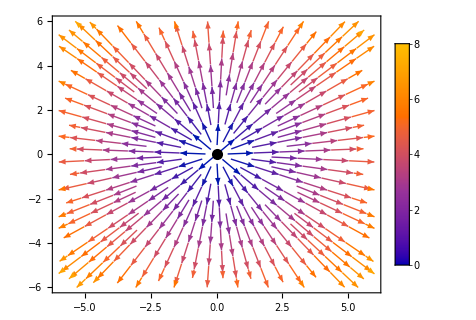

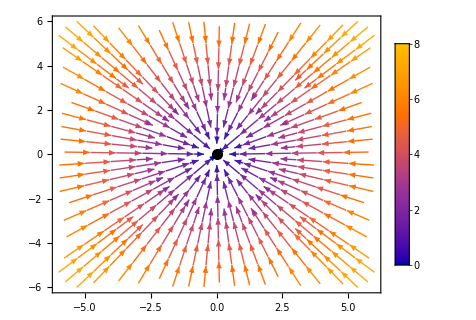

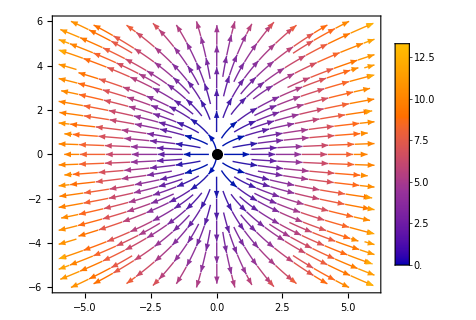

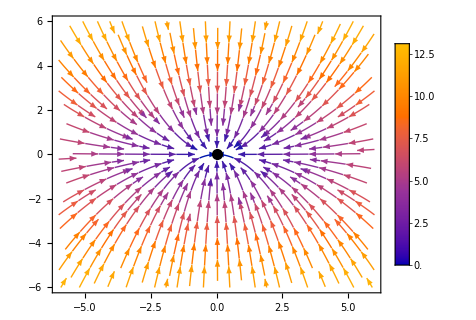

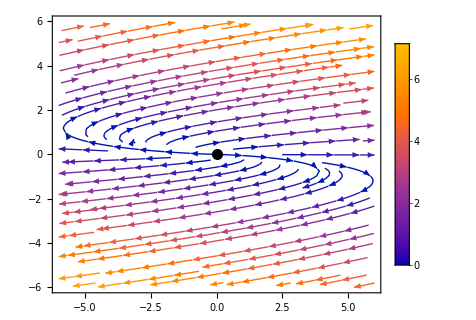

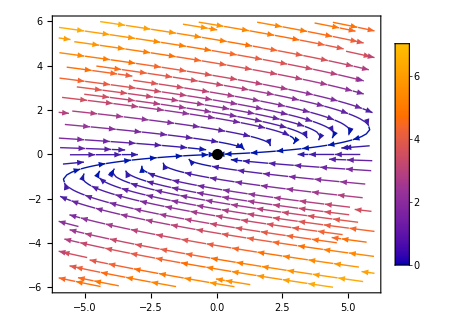

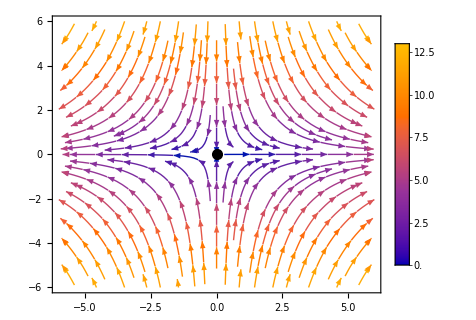

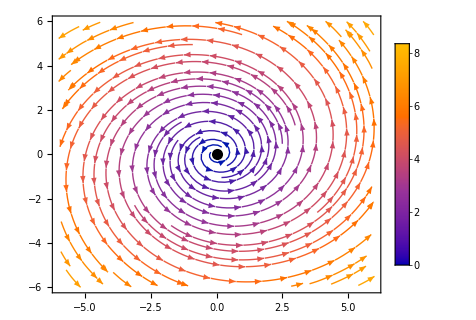

```mathematica
StreamPlot[{x,y},{x,-6,6},{y,-6,6},Epilog->{PointSize[0.02],Point[{0,0}]},PlotLegends->Automatic,AspectRatio->0.8,Frame->True]
StreamPlot[{-x,-y},{x,-6,6},{y,-6,6},Epilog->{PointSize[0.02],Point[{0,0}]},PlotLegends->Automatic,AspectRatio->0.8,Frame->True]
StreamPlot[{2x,1y},{x,-6,6},{y,-6,6},Epilog->{PointSize[0.02],Point[{0,0}]},PlotLegends->Automatic,AspectRatio->0.8,Frame->True]
StreamPlot[{-x,-2y},{x,-6,6},{y,-6,6},Epilog->{PointSize[0.02],Point[{0,0}]},PlotLegends->Automatic,AspectRatio->0.8,Frame->True]
StreamPlot[{0.2x+y,0.2y},{x,-6,6},{y,-6,6},Epilog->{PointSize[0.02],Point[{0,0}]},PlotLegends->Automatic,AspectRatio->0.8,Frame->True]
StreamPlot[{-0.2x+y,-0.2y},{x,-6,6},{y,-6,6},Epilog->{PointSize[0.02],Point[{0,0}]},PlotLegends->Automatic,AspectRatio->0.8,Frame->True]
StreamPlot[{x,-2y},{x,-6,6},{y,-6,6},Epilog->{PointSize[0.02],Point[{0,0}]},PlotLegends->Automatic,AspectRatio->0.8,Frame->True]
StreamPlot[{0.2x-y,x+0.2y},{x,-6,6},{y,-6,6},Epilog->{PointSize[0.02],Point[{0,0}]},PlotLegends->Automatic,AspectRatio->0.8,Frame->True]
StreamPlot[{-0.2x-y,x-0.2y},{x,-6,6},{y,-6,6},Epilog->{PointSize[0.02],Point[{0,0}]},PlotLegends->Automatic,AspectRatio->0.8,Frame->True]
StreamPlot[{-y,x},{x,-6,6},{y,-6,6},Epilog->{PointSize[0.02],Point[{0,0}]},PlotLegends->Automatic,AspectRatio->0.8,Frame->True]
```

```mathematica
alpha=-1.2;
beta=3.0;
gamma=2;
(*Vector Field Definition*)
vField[{x_,y_,z_}]:={alpha*x-beta*y,beta*x+alpha*y,gamma*z}
Show[SliceVectorPlot3D[vField[x,y,z], {z==0},{x,-2,2},{y,-2,2},{z,-2,2}],SliceVectorPlot3D[vField[x,y,z], {x^2+y^2==0.0001},{x,-2,2},{y,-2,2},{z,-2,2}]]
```

-Graphics3D-